```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]
```

/Users/pjoot/project/figures/phy485-optics

```mathematica
<<MaTeX` 

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

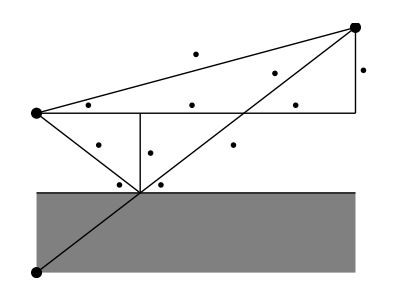

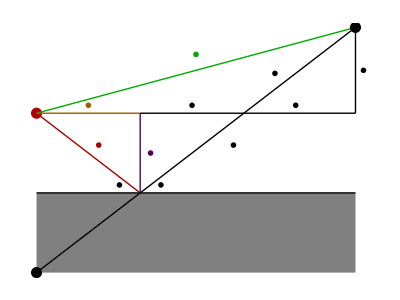

```mathematica
ClearAll[o, e1, e2, modernOpticsMidtermReflectionFig1, cmodernOpticsMidtermReflectionFig1]
o = {0,0};
e1 = {1,0};
e2 = {0,1};

f[u_, h_, L_] := Module[{sun, alpha, a, va, x, d},
sun = h e2;
va = sun + u e1;
a = va//Norm;
alpha = ArcCos[u/a];
x = L Tan[alpha] - 2 h;
p  = (h + x) e2 + L e1;
d = {x,L}//Norm;

Graphics[{Thick,
Gray,
Rectangle[-sun, L e1],
Black,
Line[{o, L e1}],
Line[{sun, sun + L e1}],
Line[{sun, p}],
Line[{-sun, p}],
Line[{sun, e1 u}],
Line[{u e1, u e1 + h e2}],
Line[{L e1 + h e2, L e1 + (h + x) e2}],
PointSize -> 0.02,
Point[sun],
Point[-sun],
Point[p],
Text[MaTeX["h"], 1.1 u e1 + (h/2) e2],
Text[MaTeX["a"], 1.2/2 u e1 + (1.2 h/2) e2],
Text[MaTeX["u"], 1/2 u e1 + (1.1 h) e2],
Text[MaTeX["u"], 3/2 u e1 + (1.1 h) e2],
Text[MaTeX["L - 2 u"], 5/2 u e1 + (1.1 h) e2],
Text[MaTeX["x"], (L + 0.1) e1 + (h + 0.5 x) e2],
Text[MaTeX["\\alpha"], 0.8 u e1 + 0.1 e2 ],
Text[MaTeX["\\alpha"], 1.2 u e1 + 0.1 e2 ],
Text[MaTeX["d"], (L/2)e1 + (x/2 + h + 0.2)e2 ],
Text[MaTeX["b_1 = a"], (0.4 +3/2) u e1 + (1.2 h/2) e2],
Text[MaTeX["b_2"], (-0.2 +2.5) u e1 + (3 h/2) e2]
}]
]

modernOpticsMidtermReflectionFig1 = f[1.3, 1, 4]

fc[u_, h_, L_] := Module[{sun, alpha, a, va, x, d},
sun = h e2;
va = sun + u e1;
a = va//Norm;
alpha = ArcCos[u/a];
x = L Tan[alpha] - 2 h;
p  = (h + x) e2 + L e1;
d = {x,L}//Norm;

Graphics[{Thick,
Gray,
Rectangle[-sun, L e1],
Black,
PointSize -> 0.02,
Line[{o, L e1}],

Red //Darker,
Point[sun],
Line[{sun, e1 u}],
Text[MaTeX["\\color{RedDarker}a"], 1.2/2 u e1 + (1.2 h/2) e2],

Purple//Darker,
Line[{u e1, u e1 + h e2}],
Text[MaTeX["\\color{PurpleDarker}h"], 1.1 u e1 + (h/2) e2],

Green//Darker,
Line[{sun, p}],
Text[MaTeX["\color{GreenDarker}d"], (L/2)e1 + (x/2 + h + 0.2)e2 ],


Orange //Darker,
Line[{sun, sun + u e1}],
Text[MaTeX["\\color{OrangeDarker}u"], 1/2 u e1 + (1.1 h) e2],

Black,
Point[-sun],
Point[p],

Line[{sun + u e1,sun + 2 u e1}],
Line[{sun + 2 u e1, sun + L e1}],
Line[{-sun, p}],
Line[{L e1 + h e2, L e1 + (h + x) e2}],

Text[MaTeX["u"], 3/2 u e1 + (1.1 h) e2],
Text[MaTeX["L - 2 u"], 5/2 u e1 + (1.1 h) e2],
Text[MaTeX["x"], (L + 0.1) e1 + (h + 0.5 x) e2],
Text[MaTeX["\\alpha"], 0.8 u e1 + 0.1 e2 ],
Text[MaTeX["\\alpha"], 1.2 u e1 + 0.1 e2 ],
Text[MaTeX["b_1 = a"], (0.4 +3/2) u e1 + (1.2 h/2) e2],
Text[MaTeX["b_2"], (-0.2 +2.5) u e1 + (3 h/2) e2]
}]
]

cmodernOpticsMidtermReflectionFig1 = fc[1.3, 1, 4]
```

```mathematica
peeters`exportForLatex["bw/modernOpticsMidtermReflectionFig1", modernOpticsMidtermReflectionFig1]
```

{bw/modernOpticsMidtermReflectionFig1.eps,bw/modernOpticsMidtermReflectionFig1pn.png}

```mathematica
peeters`exportForLatex["color/modernOpticsMidtermReflectionFig1", cmodernOpticsMidtermReflectionFig1]
```

{color/modernOpticsMidtermReflectionFig1.eps,color/modernOpticsMidtermReflectionFig1pn.png}